# Eigenfunctions of the 2D KFlow

## With large scale drag

So the linear operator of the system reads

```mathematica
ℒ[R_,α_]:={{-(1+ α^2)^2/R, α/2(α^2-1), 0},{-α^3/2, -α^4/R -μ α^2 , α^3/2},{0, -α/2(α^2-1), -(1+α^2)^2/R}} 
Subscript[R, c][α_,  μ_]:=(μ+2 α^2 μ+ α^4 μ+√((1+α^2)^2 (-2 α^6+μ^2+2 α^2 μ^2+α^4 (2+μ^2))))/(α^2(1-α^2))
```

```mathematica
Eigensystem[ℒ[R,α]]
```

{{-((1+α^2)^2)/R,(-R-2 R α^2-2 R α^4-R^2 α^2 μ-√(-R^2 (-1-4 α^2-4 α^4-2 R^2 α^4+2 R^2 α^6+2 R α^2 μ+4 R α^4 μ-R^2 α^4 μ^2)))/(2 R^2),(-R-2 R α^2-2 R α^4-R^2 α^2 μ+√(-R^2 (-1-4 α^2-4 α^4-2 R^2 α^4+2 R^2 α^6+2 R α^2 μ+4 R α^4 μ-R^2 α^4 μ^2)))/(2 R^2)},{{1,0,1},{-1,-(R+2 R α^2-R^2 α^2 μ-√(-R^2 (-1-4 α^2-4 α^4-2 R^2 α^4+2 R^2 α^6+2 R α^2 μ+4 R α^4 μ-R^2 α^4 μ^2)))/(R^2 α (-1+α^2)),1},{-1,-(R+2 R α^2-R^2 α^2 μ+√(-R^2 (-1-4 α^2-4 α^4-2 R^2 α^4+2 R^2 α^6+2 R α^2 μ+4 R α^4 μ-R^2 α^4 μ^2)))/(R^2 α (-1+α^2)),1}}}

```mathematica
λ1[R_,α_, μ_] =(-R-2 R α^2-2 R α^4-R^2 α^2 μ-√(-R^2 (-1-4 α^2-4 α^4-2 R^2 α^4+2 R^2 α^6+2 R α^2 μ+4 R α^4 μ-R^2 α^4 μ^2)))/(2 R^2);

λ2[R_,α_, μ_] =(-R-2 R α^2-2 R α^4-R^2 α^2 μ+√(-R^2 (-1-4 α^2-4 α^4-2 R^2 α^4+2 R^2 α^6+2 R α^2 μ+4 R α^4 μ-R^2 α^4 μ^2)))/(2 R^2);
```

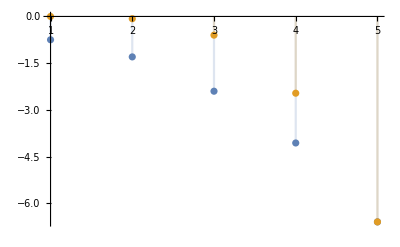

```mathematica
DiscretePlot[{Re[λ1[Subscript[R, c][1/3,0],n/3, 0]],Re[λ2[Subscript[R, c][1/3,0],n/3, 0]]},{n, 1,5}]
```

```mathematica
c1[R_,α_, μ_]=-(R+2 R α^2-R^2 α^2 μ-√(-R^2 (-1-4 α^2-4 α^4-2 R^2 α^4+2 R^2 α^6+2 R α^2 μ+4 R α^4 μ-R^2 α^4 μ^2)))/(R^2 α (-1+α^2));
c2[R_,α_, μ_]=-(R+2 R α^2-R^2 α^2 μ+√(-R^2 (-1-4 α^2-4 α^4-2 R^2 α^4+2 R^2 α^6+2 R α^2 μ+4 R α^4 μ-R^2 α^4 μ^2)))/(R^2 α (-1+α^2));
```

```mathematica
Rc = Subscript[R, c][1/3,  0];
```

```mathematica
Limit[c2[Rc, n /3, 0], n->6]
```

-1/30 ⅈ (-27 ⅈ+√1671)

```mathematica
c2[R,a, u] // FortranForm
```

-((R + 2*a**2*R - a**2*R**2*u + Sqrt(-(R**2*(-1 - 4*a**2 - 4*a**4 - 2*a**4*R**2 + 2*a**6*R**2 + 2*a**2*R*u + 4*a**4*R*u - a**4*R**2*u**2))))/(a*(-1 + a**2)*R**2))